### Wave Functions and Probability

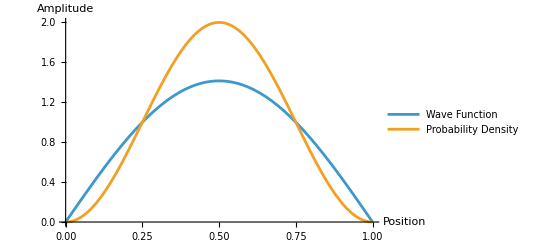

```mathematica
(*Visualizing a 1D particle in a box wave function*)
n=1; (*quantum number*)
L=1; (*box length*)
ψ[x_,n_,L_]:=Sqrt[2/L] Sin[n π x/L]
prob[x_,n_,L_]:=ψ[x,n,L]^2

Plot[{ψ[x,n,L],prob[x,n,L]},{x,0,L},PlotLegends->{"Wave Function","Probability Density"},PlotRange->All,AxesLabel->{"Position","Amplitude"}]
```